## Main analysis

initial P = 150, initial Q (MT) = 100

```mathematica
demand[P_,ϵdemand_,initialP_,initialQ_]:=Module[{q,A},A=a/.Flatten[NSolve[initialQ==a initialP^ϵdemand,WorkingPrecision->30]];q=A P^ϵdemand;Return[q]];supply[P_,ϵsupply_,initialP_,initialQ_]:=Module[{q,A},A=a/.Flatten[NSolve[initialQ==a initialP^ϵsupply,WorkingPrecision->30]];q=A P^ϵsupply;Return[q]];ReboundRatio[initialP_,initialQ_,wasteavoided_,lossavoided_,ϵsupply_,ϵdemand_]:=Module[{supply1,supply2,demand1,demand2,Q2,P2,reboundratio},supply1=supply[p,ϵsupply,initialP,initialQ];demand1=demand[p,ϵdemand,initialP,initialQ];supply2=supply1+lossavoided;demand2=demand1-wasteavoided;P2=p/.Flatten[NSolve[demand2==supply2,WorkingPrecision->30]];Q2 = demand2/.p->P2;reboundratio=((Q2-initialQ)+wasteavoided)/(wasteavoided+lossavoided);Return[reboundratio]];
```

```mathematica
demand[p,-0.5,150,100]
```

1224.74487139158895044130576217/p^0.5

```mathematica
supply[p,0.5,150,100]
```

8.16496580927726052138925237357 p^0.5

```mathematica
ReboundRatio[150,100,10,10,0.4,-0.6]
```

0.623326

```mathematica
data=Partition[Flatten[Table[{ϵsupply,ϵdemand,100*ReboundRatio[150,100,10,10,ϵsupply,ϵdemand]},{ϵsupply,0.25,0.7,0.05},{ϵdemand,-1.1,-0.3,0.1}]],3];
```

```mathematica
<<ColorBrewer`
```

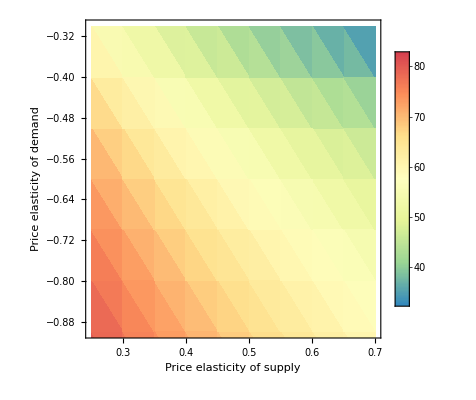

```mathematica
Fig4bottom=ListDensityPlot[data,FrameStyle->Black,FrameLabel->{"Price elasticity of supply","Price elasticity of demand"},LabelStyle->Directive[Black,Font->"Arial",FontSize->14],ColorFunction->CreateColorFunction[Spectral,7,True],PlotLegends->Automatic,PlotRange->{{0.25,0.7},{-0.9,-0.3},{30,90}}]
```

```mathematica
Module[{directory=SystemDialogInput["Directory"]},If[directory=!=$Canceled,SetDirectory[directory]]] (*generates a dialog box allowing you to set the working directory. Set it where the data file "Hfoodwaste-fig4b.csv" is saved*)
```

/Users/mburgess/Desktop/Hegwood-food-waste/final-Mathematica-files

```mathematica
foodtype= Transpose[Delete[ Import["Supplementary Data 5.csv","Table","FieldSeparators"->{","}],1]]⟦1⟧;incomegroup= Transpose[Delete[ Import["Supplementary Data 5.csv","Table","FieldSeparators"->{","}],1]]⟦2⟧;supplyelasticites= Transpose[Delete[ Import["Supplementary Data 5.csv","Table","FieldSeparators"->{","}],1]]⟦3⟧;demandelasticites= Transpose[Delete[ Import["Supplementary Data 5.csv","Table","FieldSeparators"->{","}],1]]⟦4⟧;demandelasticitytype= Transpose[Delete[ Import["Supplementary Data 5.csv","Table","FieldSeparators"->{","}],1]]⟦6⟧;data2=Transpose[{foodtype,incomegroup,supplyelasticites,demandelasticites,demandelasticitytype}];dataraw=Transpose[{supplyelasticites,demandelasticites}];
```

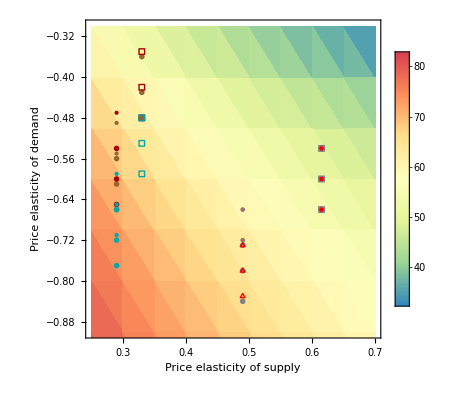

```mathematica
Fig4b=Show[Fig4bottom,
ListPlot[{dataraw⟦1⟧,dataraw⟦19⟧,dataraw⟦37⟧},PlotMarkers->▵,PlotStyle->Directive[Brown,PointSize[Large]],Frame->True,FrameStyle->Black,FrameLabel->{"Price elasticity of supply","Price elasticity of demand"},LabelStyle->Directive[Black,Font->"Arial",FontSize->14],PlotRange->{{0.25,0.7},{-1.05,-0.3}}](*Cereals and roots & tubers, Low income*),
ListPlot[{dataraw⟦7⟧,dataraw⟦26⟧,dataraw⟦43⟧},PlotStyle->Directive[Brown,PointSize[Large]],Frame->True,FrameStyle->Black,FrameLabel->{"Price elasticity of supply","Price elasticity of demand"},LabelStyle->Directive[Black,Font->"Arial",FontSize->14],PlotRange->{{0.25,0.7},{-1.05,-0.3}}](*Cereals and roots & tubers, Middle income*),
ListPlot[{dataraw⟦13⟧,dataraw⟦31⟧,dataraw⟦49⟧},PlotMarkers->▢,PlotStyle->Directive[Brown,PointSize[Large]],Frame->True,FrameStyle->Black,FrameLabel->{"Price elasticity of supply","Price elasticity of demand"},LabelStyle->Directive[Black,Font->"Arial",FontSize->14],PlotRange->{{0.25,0.7},{-1.05,-0.3}}](*Cereals and roots & tubers, High income*),ListPlot[{dataraw⟦3⟧,dataraw⟦21⟧,dataraw⟦39⟧},PlotMarkers->▵,PlotStyle->Directive[Darker[Red],PointSize[Large]],Frame->True,FrameStyle->Black,FrameLabel->{"Price elasticity of supply","Price elasticity of demand"},LabelStyle->Directive[Black,Font->"Arial",FontSize->14],PlotRange->{{0.25,0.7},{-1.05,-0.3}}](*Oilcrops & pulses, Low income*),
ListPlot[{dataraw⟦9⟧,dataraw⟦27⟧,dataraw⟦45⟧},PlotStyle->Directive[Darker[Red],PointSize[Large]],Frame->True,FrameStyle->Black,FrameLabel->{"Price elasticity of supply","Price elasticity of demand"},LabelStyle->Directive[Black,Font->"Arial",FontSize->14],PlotRange->{{0.25,0.7},{-1.05,-0.3}}](*Oilcrops & pulses, Middle income*),
ListPlot[{dataraw⟦15⟧,dataraw⟦33⟧,dataraw⟦51⟧},PlotMarkers->□,PlotStyle->Directive[Darker[Red],PointSize[Large]],Frame->True,FrameStyle->Black,FrameLabel->{"Price elasticity of supply","Price elasticity of demand"},LabelStyle->Directive[Black,Font->"Arial",FontSize->14],PlotRange->{{0.25,0.7},{-1.05,-0.3}}](*Oilcrops & pulses, High income*),ListPlot[{dataraw⟦4⟧,dataraw⟦22⟧,dataraw⟦40⟧},PlotMarkers->▵,PlotStyle->Directive[Darker[Cyan],PointSize[Large]],Frame->True,FrameStyle->Black,FrameLabel->{"Price elasticity of supply","Price elasticity of demand"},LabelStyle->Directive[Black,Font->"Arial",FontSize->14],PlotRange->{{0.25,0.7},{-1.05,-0.3}}](*Fruits & vegetables, Low income*),
ListPlot[{dataraw⟦10⟧,dataraw⟦28⟧,dataraw⟦46⟧},PlotStyle->Directive[Darker[Cyan],PointSize[Large]],Frame->True,FrameStyle->Black,FrameLabel->{"Price elasticity of supply","Price elasticity of demand"},LabelStyle->Directive[Black,Font->"Arial",FontSize->14],PlotRange->{{0.25,0.7},{-1.05,-0.3}}](*Fruits & vegetables, Middle income*),
ListPlot[{dataraw⟦16⟧,dataraw⟦34⟧,dataraw⟦52⟧},PlotMarkers->□,PlotStyle->Directive[Darker[Cyan],PointSize[Large]],Frame->True,FrameStyle->Black,FrameLabel->{"Price elasticity of supply","Price elasticity of demand"},LabelStyle->Directive[Black,Font->"Arial",FontSize->14],PlotRange->{{0.25,0.7},{-1.05,-0.3}}](*Fruits & vegetables, High income*),ListPlot[{dataraw⟦5⟧,dataraw⟦23⟧,dataraw⟦41⟧},PlotMarkers->△,PlotStyle->Directive[Red,PointSize[Large]],Frame->True,FrameStyle->Black,FrameLabel->{"Price elasticity of supply","Price elasticity of demand"},LabelStyle->Directive[Black,Font->"Arial",FontSize->14],PlotRange->{{0.25,0.7},{-1.05,-0.3}}](*Meat, Low income*),
ListPlot[{dataraw⟦11⟧,dataraw⟦29⟧,dataraw⟦47⟧},PlotStyle->Directive[Red,PointSize[Large]],Frame->True,FrameStyle->Black,FrameLabel->{"Price elasticity of supply","Price elasticity of demand"},LabelStyle->Directive[Black,Font->"Arial",FontSize->14],PlotRange->{{0.25,0.7},{-1.05,-0.3}}](*Meat, Middle income*),
ListPlot[{dataraw⟦17⟧,dataraw⟦35⟧,dataraw⟦53⟧},PlotMarkers->▢,PlotStyle->Directive[Red,PointSize[Large]],Frame->True,FrameStyle->Black,FrameLabel->{"Price elasticity of supply","Price elasticity of demand"},LabelStyle->Directive[Black,Font->"Arial",FontSize->14],PlotRange->{{0.25,0.7},{-1.05,-0.3}}](*Meat, High income*),ListPlot[{dataraw⟦6⟧,dataraw⟦24⟧,dataraw⟦42⟧},PlotMarkers->▵,PlotStyle->Directive[Gray,PointSize[Large]],Frame->True,FrameStyle->Black,FrameLabel->{"Price elasticity of supply","Price elasticity of demand"},LabelStyle->Directive[Black,Font->"Arial",FontSize->14],PlotRange->{{0.25,0.7},{-1.05,-0.3}}](*Milk, Low income*),
ListPlot[{dataraw⟦12⟧,dataraw⟦30⟧,dataraw⟦48⟧},PlotStyle->Directive[Gray,PointSize[Medium]],Frame->True,FrameStyle->Black,FrameLabel->{"Price elasticity of supply","Price elasticity of demand"},LabelStyle->Directive[Black,Font->"Arial",FontSize->14],PlotRange->{{0.25,0.7},{-1.05,-0.3}}](*Milk, Middle income*),
ListPlot[{dataraw⟦18⟧,dataraw⟦36⟧,dataraw⟦54⟧},PlotMarkers->□,PlotStyle->Directive[Gray,PointSize[Large]],Frame->True,FrameStyle->Black,FrameLabel->{"Price elasticity of supply","Price elasticity of demand"},LabelStyle->Directive[Black,Font->"Arial",FontSize->14],PlotRange->{{0.25,0.7},{-1.05,-0.3}}](*Milk, High income*)
]
```

```mathematica
Export["hegwood-foodwaste-fig4b.pdf", %]
```

hegwood-foodwaste-fig4b.pdf

## Sensitivity analysis to costs

```mathematica
ReboundRatioCosts[initialP_,initialQ_,wasteavoided_,lossavoided_,ϵsupply_,ϵdemand_,costlossavoidedpcteqp_,costwasteavoidedpcteqp_]:=Module[{supply1,supply2,demand1,demand2,Q2,P2,reboundratio},supply1=supply[p,ϵsupply,initialP,initialQ];demand1=demand[p,ϵdemand,initialP,initialQ];supply2=supply[p-(initialP costlossavoidedpcteqp/100),ϵsupply,initialP,initialQ]+lossavoided;demand2=demand[p+(initialP costwasteavoidedpcteqp/100),ϵdemand,initialP,initialQ]-wasteavoided;P2=p/.Flatten[NSolve[demand2==supply2,WorkingPrecision->30]];Q2 = demand2/.p->P2;reboundratio=((Q2-initialQ)+wasteavoided)/(wasteavoided+lossavoided);Return[reboundratio]];
```

```mathematica
ReboundRatioCosts[150,100,10,10,0.4,-0.6,0,0]
```

0.623326

```mathematica
datahigh=Table[{x,100ReboundRatioCosts[150,100,10,10,0.3,-1,x,0]},{x,0,50,10}];datamedium=Table[{x,100ReboundRatioCosts[150,100,10,10,0.5,-0.7,x,0]},{x,0,50,10}];datalow=Table[{x,100ReboundRatioCosts[150,100,10,10,0.6,-0.5,x,0]},{x,0,50,10}];
```

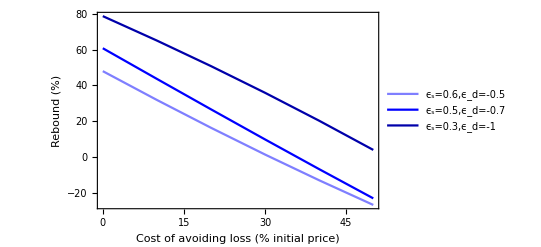

```mathematica
reboundscosts=ListLinePlot[{datalow,datamedium,datahigh},Frame->True,FrameStyle->Black,FrameLabel->{"Cost of avoiding loss (% initial price)","Rebound (%)"},LabelStyle->Directive[Black,Font->"Arial",FontSize->14],PlotStyle->{Directive[Blue,Opacity[0.5]],Blue,Darker[Blue]},PlotLegends->{"ϵ_s=0.6,ϵ_d=-0.5","ϵ_s=0.5,ϵ_d=-0.7","ϵ_s=0.3,ϵ_d=-1"}]
```

```mathematica
TrueConsumptionCosts[initialP_,initialQ_,wasteavoided_,lossavoided_,ϵsupply_,ϵdemand_,costlossavoidedpcteqp_,costwasteavoidedpcteqp_]:=Module[{supply1,supply2,demand1,demand2,Q2,P2,consumptionchange},supply1=supply[p,ϵsupply,initialP,initialQ];demand1=demand[p,ϵdemand,initialP,initialQ];supply2=supply[p-(initialP costlossavoidedpcteqp/100),ϵsupply,initialP,initialQ]+lossavoided;demand2=demand[p+(initialP costwasteavoidedpcteqp/100),ϵdemand,initialP,initialQ]-wasteavoided;P2=p/.Flatten[NSolve[demand2==supply2,WorkingPrecision->30]];Q2 = demand2/.p->P2;consumptionchange=100(((Q2-initialQ)+wasteavoided)/initialQ);Return[consumptionchange]];
```

```mathematica
TrueConsumptionCosts[150,100,10,10,0.4,-0.6,20,0]
```

6.63078

```mathematica
datahigh2=Table[{x,TrueConsumptionCosts[150,100,10,10,0.3,-1,x,0]},{x,0,50,10}];datamedium2=Table[{x,TrueConsumptionCosts[150,100,10,10,0.5,-0.7,x,0]},{x,0,50,10}];datalow2=Table[{x,TrueConsumptionCosts[150,100,10,10,0.6,-0.5,x,0]},{x,0,50,10}];
```

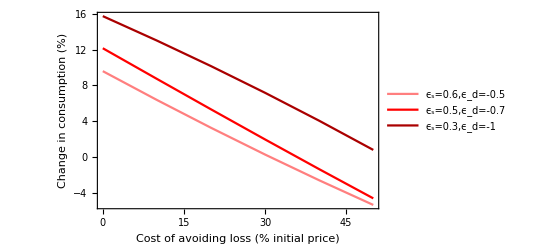

```mathematica
consumptioncosts=ListLinePlot[{datalow2,datamedium2,datahigh2},Frame->True,FrameStyle->Black,FrameLabel->{"Cost of avoiding loss (% initial price)","Change in consumption (%)"},LabelStyle->Directive[Black,Font->"Arial",FontSize->14],PlotStyle->{Directive[Red,Opacity[0.5]],Red,Darker[Red]},PlotLegends->{"ϵ_s=0.6,ϵ_d=-0.5","ϵ_s=0.5,ϵ_d=-0.7","ϵ_s=0.3,ϵ_d=-1"}]
```

```mathematica
GraphicsRow[{reboundscosts,consumptioncosts}]
```